```mathematica
SetDirectory["/Users/sinbi/desktop/STUDY/Data_get/gg"];
Needs["ErrorBarPlots`"];
Get["/Users/sinbi/desktop/STUDY/Data_get/ErrorBarLogPlots.m"];
Get["/Users/sinbi/desktop/STUDY/Data_get/ProtonFluxELDRAnn.m"];
```

## AMS02-Experiment Error Bar Import

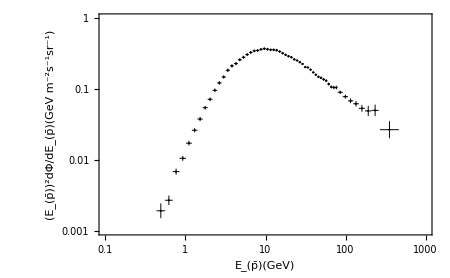

```mathematica
IErrorg= Import["/Users/sinbi/desktop/study/Data_get/Error_data_AMS02_Full.dat","Table",HeaderLines-> 1];
Length[IErrorg];
IErrorg1=Table[{IErrorg[[i,1]],IErrorg[[i,2]],(IErrorg[[i,4]]-IErrorg[[i,3]])/2,(IErrorg[[i,6]]-IErrorg[[i,5]])/2},{i,1,Length[IErrorg]}];
IErrorg2=IErrorg1/.{x_,y_,z_,k_}->{{x,y},ErrorBar[z,k]};
ErroPlotg=ErrorListLogLogPlot[IErrorg2,Frame->True,Axes->False,PlotRange->{{10^-1,10^3},{10^-3,1}}, ErrorBarFunction->Automatic,ImageSize->450,PlotStyle->{Black,AbsolutePointSize[1.5],AbsoluteThickness[0.7]},FrameLabel->{"E_(p̄)(GeV)","(E_(p̄))^2dΦ/dE_(p̄)(GeV m^-2s^-1sr^-1)"}]
```

## Get Background(BG)

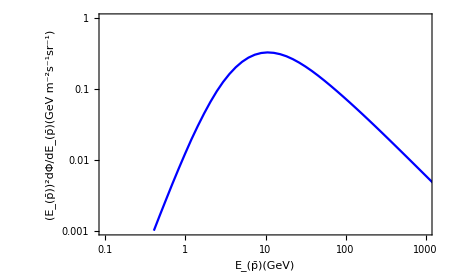

```mathematica
BGg=Import["/Users/sinbi/desktop/study/Data_get/AMSMD.dat","Table","HearderLines"->1];
Length[BGg];
ifBGg=Interpolation[BGg];
BGPlotg=ListLogLogPlot[ifBGg,Joined->True,Axes->False,Frame->True,PlotRange->{{10^-1,10^3},{10^-3,1}},ImageSize->450,PlotStyle->{Blue},FrameLabel->{"E_(p̄)(GeV)","(E_(p̄))^2dΦ/dE_(p̄)(GeV m^-2s^-1sr^-1)"}]
```

## Dark Matter(DM)

```mathematica
primaryg="g";
halog="Ein";
propagationg="MAX";
mDMg=100;
σvg=0.7*10^-26;
Eγ=10^lEγ;
```

```mathematica
ifPog=Interpolation[Table[{10^lEγ,10^lEγ 10.^ ProtonFluxELDRAnn[primaryg, halog, propagationg][mDMg, σvg,Log[10,10^lEγ]]},{lEγ,-1,3,0.01}]];
```

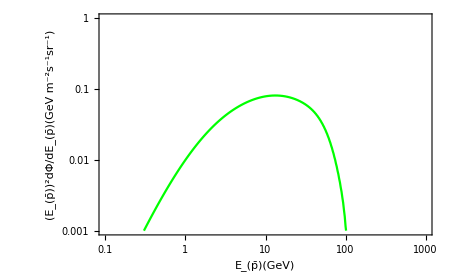

```mathematica
PlotMEDg=ListLogLogPlot[ifPog,PlotRange->{{10^-1,10^3},{10^-3,1}},Joined->True,PlotStyle->Green,Frame->True,Axes->False,ImageSize->450,FrameTicks-> Automatic, FrameLabel->{"E_(p̄)(GeV)","(E_(p̄))^2dΦ/dE_(p̄)(GeV m^-2s^-1sr^-1)"}]
```

## SUM=BG+DM

InterpolatingFunction[…]

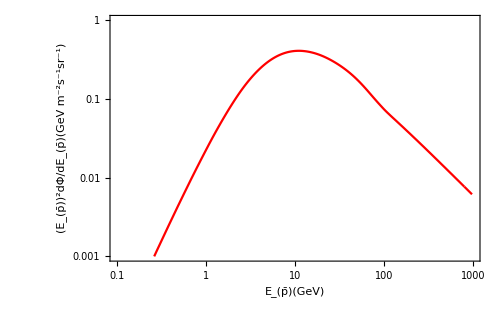

```mathematica
Sumdatag=Interpolation[Table[{x,ifBGg[x]+ifPog[x]},{x,0.18,10^2.99,0.1}]]
SumPlotg=ListLogLogPlot[Sumdatag,Joined->True,PlotRange->{{10^-1,10^3},{10^-3,1}},PlotStyle->Red,Frame->True,Axes->False,ImageSize->500 ,FrameLabel->{"E_(p̄)(GeV)","(E_(p̄))^2dΦ/dE_(p̄)(GeV m^-2s^-1sr^-1)"}]
```

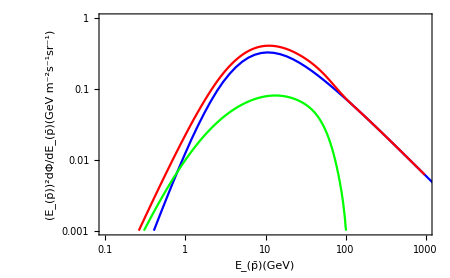

```mathematica
Show[BGPlotg,PlotMEDg,SumPlotg]
```

## χ^2- Fitting

```mathematica
SumYg=Table[Sumdatag[IErrorg1[[i,1]]],{i,Length[IErrorg]}];
IErrorYg=Flatten[Table[{IErrorg1[[i,2]]},{i,1,Length[IErrorg]}],1];
IErrorSizeg=Flatten[Table[{IErrorg1[[i,4]]},{i,1,Length[IErrorg]}],1];chiSUMg=((SumYg-IErrorYg)/IErrorSizeg)^2;
Sumg1=Sum[chiSUMg[[i]],{i,1,Length[IErrorg]}]
Re[Sumg1]
```

1601.78

1601.78

## Mass-σv graph

```mathematica
ClearAll[σv02]
```

```mathematica
mDM02=10^lmDM02;
```

```mathematica
σv02=10^lσv02;
```

```mathematica
ifPog2=Interpolation[Table[{10^lEγ,10^lEγ 10.^ ProtonFluxELDRAnn[primaryg, halog, propagationg][mDM02, σv02,Log[10,10^lEγ]]},{lEγ,-1,3,0.01}]];
```

```mathematica
Sumdatag2=Interpolation[Table[{x,ifBGg[x]+ifPog2[x]},{x,0.18,10^2.99,0.1}]];
SumYg2=Table[Sumdatag2[IErrorg1[[i,1]]],{i,Length[IErrorg]}];
chiSUMg2=((SumYg2-IErrorYg)/IErrorSizeg)^2;
FinalSumg=Sum[chiSUMg2[[i]],{i,1,Length[IErrorg]}];
```

```mathematica
contg=Flatten[Table[Re[{mDM02,lσv02,σv02,FinalSumg}],{lmDM02,0.7,2.4,0.02},{lσv02,-28,-25,0.05}], 1];
Export["gg_EIN_MAX.dat",contg,"Table"];
```

```mathematica
contableg=Import["//Users/sinbi/desktop/study/Data_get/gg/gg_EIN_MAX.dat","Table",HeaderLines->1]
```

{{5.01187,-27.95,1.12202×10^-28,3750.08},{5.01187,-27.9,1.25893×10^-28,4717.88},5241,{251.189,-25.05,8.91251×10^-26,41927.7},{251.189,-25.,1.×10^-25,53055.7}}
 |  |  |  |

```mathematica
contgLog=Table[{contableg[[i,1]],contableg[[i,2]], contableg[[i, 4]]},{i, Length[contableg]}];
```

```mathematica
Export["gg_table_EIN_MAX.dat",contgLog,"Table"]
```

gg_table_EIN_MAX.dat

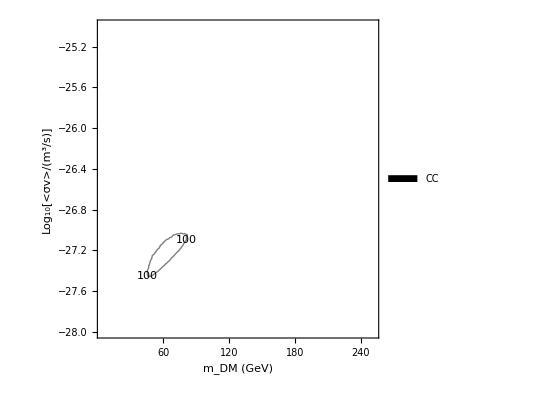

```mathematica
ListContourPlot[contgLog,Contours-> {60, 70,80,100},
FrameLabel->{"m_DM (GeV)","Log_10[<σv>/(m^3/s)]"}, ContourLabels->All,ContourShading->None,PlotLegends->Placed[SwatchLegend[{"CC"},LegendMarkerSize->20],Right]]
```